```mathematica
Demonstration of Affine.m usage
```

```mathematica
First we need to setup path and load the package
```

```mathematica
AppendTo[$Path,NotebookDirectory[] <> "../src/"];
<<affine.m;
```

```mathematica
Or we can run unit tests to see that package works correctly:
```

```mathematica
AppendTo[$Path,NotebookDirectory[] <> "../tests/"];
<<tests.m;
```

All tests completed

```mathematica
OverHat[Subscript[A,1]][simpleRoot][1]
```

affineWeight[2,finiteWeight[2,{1,-1}],0,0]

```mathematica
makeAffineWeight[{1,-1},0,0]
```

affineWeight[2,finiteWeight[2,{1,-1}],0,0]

```mathematica
Weights
```

```mathematica
We review basic datastructures. 
finiteWeight and affineWeight are used to represent weights of finite-dimensional and 
affine Lie algebra weights correspondingly.  We have following generic constructors:
```

makeFiniteWeight[{1,2,3}]

finiteWeight[3,{1,2,3}]

```mathematica
Here the argument of constructor is the list of coordinates in orthogonal basis.
Constructor for affine LIe algebra weights is similar but it also needs level and grade of weight.
```

aw=makeAffineWeight[{1, 2}, 2, 3]

affineWeight[2,finiteWeight[2,{1,2}],2,3]

```mathematica
We can get level and grade of affine weight with the functions:
```

```mathematica
level[aw]
```

2

```mathematica
grade[aw]
```

3

```mathematica
We can add and multiply weights by numbers.
```

```mathematica
makeFiniteWeight[{1,2}]+2*makeFiniteWeight[{1,1}]
```

finiteWeight[2,{3,4}]

```mathematica
Root systems
```

```mathematica
Now we can introduce root systems. We can specify root system by hand by listing the set of simple roots. For example to specify the root system of algebra Subscript[B, 2] (so(5)) we can use this code:
```

```mathematica
makeFiniteRootSystem[{makeFiniteWeight[{1,-1}],makeFiniteWeight[{0,1}]}]
```

finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}]

```mathematica
Or in more concise form:
```

```mathematica
rs=makeFiniteRootSystem[{{1,-1},{0,1}}]
```

finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}]

```mathematica
Root systems of (non-twisted) affine Lie algebras are constructed as 
affine extensions of finite-dimensional ones:
```

```mathematica
makeAffineExtension[rs]
```

affineRootSystem[2,finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}],affineWeight[2,finiteWeight[2,{-1,-1}],0,1],{affineWeight[2,finiteWeight[2,{1,-1}],0,0],affineWeight[2,finiteWeight[2,{0,1}],0,0]}]

```mathematica
We have special constructors for root systems of simple Lie algebras. Long form is
```

```mathematica
makeSimpleRootSystem[C,3]
```

finiteRootSystem[3,3,{finiteWeight[3,{1,-1,0}],finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,0,2}]}]

```mathematica
Concise form is just
```

```mathematica
Subscript[C, 3]
```

finiteRootSystem[3,3,{finiteWeight[3,{1,-1,0}],finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,0,2}]}]

```mathematica
Now we can get some properties of root system and algebra. For example
```

```mathematica
rank[Subscript[C, 3]]
```

3

```mathematica
roots[Subscript[C, 3]]
```

{finiteWeight[3,{-2,0,0}],finiteWeight[3,{-1,-1,0}],finiteWeight[3,{-1,0,-1}],finiteWeight[3,{-1,0,1}],finiteWeight[3,{-1,1,0}],finiteWeight[3,{0,-2,0}],finiteWeight[3,{0,-1,-1}],finiteWeight[3,{0,-1,1}],finiteWeight[3,{0,0,-2}],finiteWeight[3,{0,0,2}],finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,1,1}],finiteWeight[3,{0,2,0}],finiteWeight[3,{1,-1,0}],finiteWeight[3,{1,0,-1}],finiteWeight[3,{1,0,1}],finiteWeight[3,{1,1,0}],finiteWeight[3,{2,0,0}]}

```mathematica
To specify root system of semisimple Lie algebra we can use following natural notation
```

```mathematica
Subscript[C, 3]⊕Subscript[B, 2]
```

finiteRootSystem[5,5,{finiteWeight[5,{1,-1,0,0,0}],finiteWeight[5,{0,1,-1,0,0}],finiteWeight[5,{0,0,2,0,0}],finiteWeight[5,{0,0,0,1,-1}],finiteWeight[5,{0,0,0,0,1}]}]

```mathematica
positiveRoots[Subscript[A, 1]⊕Subscript[B, 2]]
```

{finiteWeight[3,{1,0,0}],finiteWeight[3,{0,1,-1}],finiteWeight[3,{0,0,1}],finiteWeight[3,{0,1,1}],finiteWeight[3,{0,1,0}]}

```mathematica
We can use hat to specify (non-twisted) affine extension of finite-dimensional root system. 
Function cartanMatrix calculate Cartan matrix corresponding to root system.
```

```mathematica
cartanMatrix[OverHat[(Subscript[A, 3]⊕Subscript[B, 2])]]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | -1
0 | 2 | -1 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0
0 | 0 | -1 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | -1
-2 | 0 | 0 | 0 | -2 | 2)

```mathematica
cartanMatrix[Subscript[A, 2]]//MatrixForm
```

(2 | -1
-1 | 2)

```mathematica
If we specify root system we can use Dynkin labels to construct weight:
```

```mathematica
weight[Subscript[B, 2]][1,1]
```

finiteWeight[2,{3/2,1/2}]

```mathematica
Weyl group
```

```mathematica
Weyl group is generated by reflections corresponding to simple roots. So we can specify Weyl group element
by the sequence of simple reflection.
```

```mathematica
s=weylGroupElement[Subscript[B, 2]][1,2,1];
```

```mathematica
Then we can act by Weyl group element on some weight
```

```mathematica
s@weight[Subscript[B, 2]][1,1]
```

finiteWeight[2,{-3/2,1/2}]

```mathematica
It is possible to calculate Weyl group orbit of some weight. This and related functions which calculate orbits 
with the parity of Weyl group elements are of crucial importance in our approach to calculation of weight 
multiplicities in Lie algebra modules and branching coefficients.
```

```mathematica
orbit[Subscript[B, 2]][weight[Subscript[B, 2]][1,2]]
```

{{finiteWeight[2,{2,1}]},{finiteWeight[2,{1,2}],finiteWeight[2,{2,-1}]},{finiteWeight[2,{-1,2}],finiteWeight[2,{1,-2}]},{finiteWeight[2,{-2,1}],finiteWeight[2,{-1,-2}]},{finiteWeight[2,{-2,-1}]}}

```mathematica
Some times it is more convenient to look not at the coordinates in orthogonal basis, 
but at Dynkin labels of weights. So we can present previous result this way:
```

```mathematica
dynkinLabels[Subscript[B, 2]]/@Flatten[orbit[Subscript[B, 2]][weight[Subscript[B, 2]][1,2]]]
```

{{1,2},{-1,4},{3,-2},{-3,4},{3,-4},{-3,2},{1,-4},{-1,-2}}

```mathematica
Auxiliary datastructures  
Two auxiliary datastructures are important for what follows. First one is hashtable which is implemented 
with DownValues and have functions keys and values:
```

```mathematica
h=makeHashtable[{a,b,c},{1,2,3}]
```

Affine`Private`table$777

```mathematica
h[a]
```

1

```mathematica
keys[h]
```

{a,b,c}

```mathematica
values[h]
```

{1,2,3}

```mathematica
Another datastructure formalElement represents is a hashtable which has weights as the keys and 
numbers as the values. It is used to represent elements of formal exponents algebra such as module 
characters, singular elements of modules and hold branching coefficients. Addition, multiplication by
number and by exponent of weight is implemented for formal elements.
There are special accessors weights and multiplicities.
```

```mathematica
fe=makeFormalElement[{weight[Subscript[B, 2]][1,0],weight[Subscript[B, 2]][0,1]},{1,2}]
```

formalElement[Affine`Private`table$783]

```mathematica
(fe*2)[weights]
```

{finiteWeight[2,{1,0}],finiteWeight[2,{1/2,1/2}]}

```mathematica
(fe*2)[multiplicities]
```

{2,4}

```mathematica
(fe*Exp[weight[Subscript[B, 2]][1,1]])[weights]
```

{finiteWeight[2,{5/2,1/2}],finiteWeight[2,{2,1}]}

```mathematica
Modules
```

```mathematica
Lie algebra module is represented by the datastructure module. Module can be specified by 
its set of singular weights. Irreducible module possess 
Weyl group invariance while parabolic Verma module is invariant with respect to subgroup of Lie algebra
Weyl group. Verma modules are infinite-dimensional and we need to set some 
limit of computations. So generic constructor has several parameters:
```

```mathematica
vm=makeModule[Subscript[B, 2]][makeFormalElement[{weight[Subscript[B, 2]][1,1]},{1}],emptyRootSystem[],5]
```

module[finiteRootSystem[2,2,{finiteWeight[2,{1,-1}],finiteWeight[2,{0,1}]}],formalElement[Affine`Private`table$799],emptyRootSystem[],5]

```mathematica
We have just constructed Verma module of Lie algebra B2. There are special constructors for irreducible, 
Verma and parabolic Verma modules:
```

```mathematica
b2=makeSimpleRootSystem[B,2];
vm=makeVermaModule[b2][{2,1},5];
pm=makeParabolicVermaModule[b2][weight[b2][2,1],{1},5];
im=makeIrreducibleModule[b2][2,1];
```

```mathematica
Characters
```

```mathematica
Now we can demonstrate calculation of weight multiplicities in module characters. Function to calculate 
multiplicities is called character and it returns formalElement datastructure. We then can use 
some additional code to plot nice figures.
```

```mathematica
textPlot[f_formalElement]:=drawPlaneProjection[2,1,f,
{Frame->True,GridLines->Automatic,PlotRange->{{-3,3},{-3,3}}, PlotRangeClipping->True}];
```

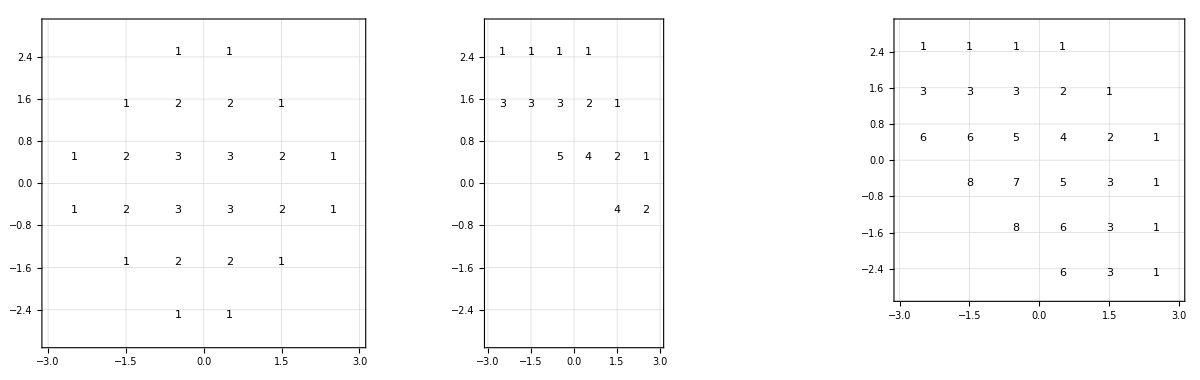

```mathematica
GraphicsRow[textPlot/@(character/@{im,vm,pm})]
```

```mathematica
Our code is generic, it works for finite-dimensional and affine Lie algebras. But we need additional routine 
to plot weight multiplicities in affine case.
```

```mathematica
affinePlot[f_formalElement,opts___?OptionQ]:=
Graphics[(Text[f[#],{grade[#],#[finitePart][standardBase][[1]]}]&)/@f[weights],opts]
```

```mathematica
Now we can plot the character of affine Lie algebra A1.
```

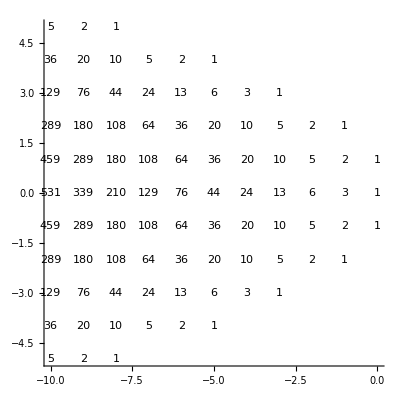

```mathematica
affinePlot[character[makeIrreducibleModule[OverHat[Subscript[A, 1]]][1,2]],{Axes->True}]
```

```mathematica
We see that result coicides with the tables in book of Moody, Patera et. al. 
Also it is easy to notice Weyl symmetry of irreducible module. So it is enough to calculate multiplicities
in main Weyl chamber only. 
This multiplicities are conveniently encoded as string functions. Affine.m has special function 
stringFunctions which calculates all string functions of module. So for A1 we can use it.
```

```mathematica
stringFunctions[OverHat[Subscript[A, 1]],{1,2}]
```

{{{1,2},1+2 q+5 q^2+10 q^3+20 q^4+36 q^5+64 q^6+108 q^7+180 q^8+289 q^9+459 q^10},{{3,0},1+3 q+6 q^2+13 q^3+24 q^4+44 q^5+76 q^6+129 q^7+210 q^8+339 q^9+531 q^10}}

```mathematica
We can get less trivial results too:
```

```mathematica
stringFunctions[OverHat[Subscript[B, 3]],{1,1,0,0}]
```

{{{0,2,0,0},q+9 q^2+51 q^3+218 q^4+789 q^5+2541 q^6+7493 q^7+20601 q^8+53499 q^9+132427 q^10},{{0,0,1,0},3 q+22 q^2+107 q^3+420 q^4+1431 q^5+4401 q^6+12514 q^7+33403 q^8+84617 q^9+205068 q^10},{{1,1,0,0},1+8 q+42 q^2+176 q^3+633 q^4+2038 q^5+6027 q^6+16646 q^7+43450 q^8+108134 q^9+258299 q^10},{{0,0,0,2},3 q+18 q^2+88 q^3+336 q^4+1149 q^5+3530 q^6+10092 q^7+27048 q^8+68919 q^9+167880 q^10},{{2,0,0,0},1+9 q+51 q^2+218 q^3+789 q^4+2541 q^5+7493 q^6+20601 q^7+53499 q^8+132427 q^9+314634 q^10}}

```mathematica
Branching
```

```mathematica
Now we can consider the problem of decomposition of irreducible modules of Lie algebra into the sum
of irreducible modules of subalgebra.
One way to specify the subalgebra is to list its simple roots in the root space of algebra. E.g.
```

```mathematica
sub=makeFiniteRootSystem[{Plus @@ Subscript[B, 2][simpleRoots]}]
```

finiteRootSystem[1,2,{finiteWeight[2,{1,0}]}]

```mathematica
To calculate branching of irreducible module to irreducible modules of subalgebra use function branching
```

```mathematica
brc=branching[makeIrreducibleModule[Subscript[B, 2]][1,1],sub]
```

formalElement[Affine`Private`table$6283]

```mathematica
In this simple case of embedding A1->B2 we can compare the results by hand. First look at the weight diagram 
the module:
```

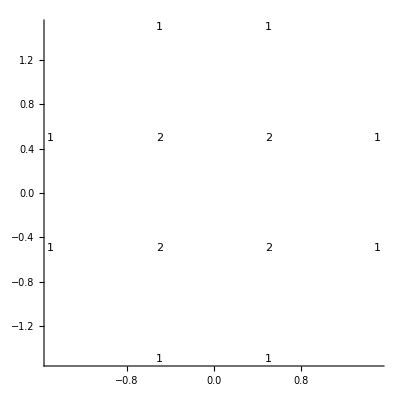

```mathematica
textPlot[makeIrreducibleModule[Subscript[B, 2]][1,1],{Axes->True}]
```

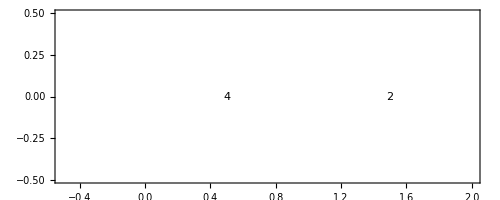

```mathematica
drawPlaneProjection[1,2,brc,{Frame->True,PlotRange->{{-0.5,2},{-0.5,0.5}}, PlotRangeClipping->True}]
```

```mathematica
The same function can be used for affine Lie algebras:
```

```mathematica
suba=makeAffineExtension[sub];
brc=branching[makeIrreducibleModule[OverHat[Subscript[B, 2]]][1,1,1],suba]
```

formalElement[Affine`Private`table$12229]

```mathematica
Now we can see branching coefficients in main Weyl chamber:
```

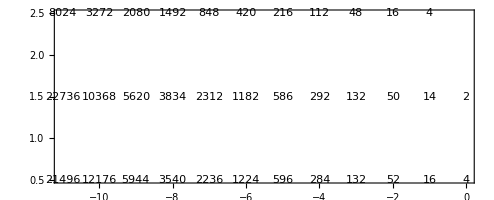

```mathematica
affinePlot[brc,{Frame->True}]
```

```mathematica
To get this result as the set of branching functions we can use function branchingFunctions, which has 
following parameters: root system of algebra, root system of subalgebra and Dynkin labels of highest weight 
of algebra module. For example to get the above result use this code:
```

```mathematica
branchingFunctions[OverHat[Subscript[B, 2]],suba,{1,1,1}]
```

{{{1,5},4 q+16 q^2+48 q^3+112 q^4+216 q^5+420 q^6+848 q^7+1492 q^8+2080 q^9+3272 q^10},{{3,3},2+14 q+50 q^2+132 q^3+292 q^4+586 q^5+1182 q^6+2312 q^7+3834 q^8+5620 q^9+10368 q^10},{{5,1},4+16 q+52 q^2+132 q^3+284 q^4+596 q^5+1224 q^6+2236 q^7+3540 q^8+5944 q^9+12176 q^10}}

```mathematica
We can see that level of modules of subalgebra are not equal to the level of module of Lie algebra since 
we have built the root system of A1-subalgebra on the short root of B2.
```